## Initializing all variables

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
scatterdata=Import["data/scatterdata.mx"];
```

```mathematica
{lengthofarray,ensemblesize,frames}=Dimensions@scatterdata
```

{26,100000,2}

Note that there are 26 different values of α, with each having 100,000 particle collisions.

```mathematica
snapcount=ensemblesize*frames;
```

```mathematica
dθ=0.02;
Table[temp=Append[Table[FirstPosition[scatterdata[[array,;;,1]],_?(#>θ&)],{θ,0.0,1-dθ,dθ}]//Flatten,(snapcount)/2];
meanscatter[[array]]=Table[Mean[scatterdata[[array,temp[[i]];;temp[[i+1]]]]],{i,1,Length@temp-1}];,{array,1,lengthofarray,1}];
Dimensions@meanscatter
```

{26,50,2}

θ_in is discretised into 50 different bins from 0 to π . All units of θ_out, θ_in are given in rad/π, such that π  ~.1c1.

```mathematica
gridsize=Length@meanscatter[[1]];
```

## 2D Collision statistics

### Initializing all variables

```mathematica
workarray=Table[i*0.25,{i,0,lengthofarray-1}];
```

```mathematica
collisionmapplain=Table[Flatten@{workarray[[i]],meanscatter[[i,j]]},{i,1,lengthofarray},{j,1,gridsize}];
collisionmapdelta=Table[{workarray[[i]],meanscatter[[i,j,1]],meanscatter[[i,j,2]]-meanscatter[[i,j,1]]},{i,1,lengthofarray},{j,1,gridsize}];
collisionmapdeltaalpha=Table[{workarray[[i]],meanscatter[[i,j,1]],meanscatter[[i,j,2]]-meanscatter[[i,j,1]]},{i,1,lengthofarray},{j,1,gridsize}];
collisionmapplainplot=Flatten[collisionmapplain,1];
collisionmapdeltaplot=Flatten[collisionmapdelta,1];
collisionmapdeltaalphaplot=Flatten[collisionmapdeltaalpha,1];
```

```mathematica
Dimensions@Flatten[scatterdata,1]
```

{2600000,2}

### Plotting

```mathematica
newStyle[x_]:=x/.l_Line:>Sequence[Opacity[.9],Thick,Dashed,Black,l]
```

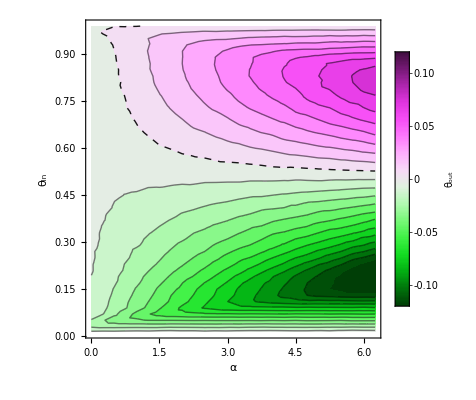

```mathematica
min=-0.12;
max=0.12;
colmap="GreenPinkTones";
colfunc=ColorData[colmap][Rescale[#,{min,max}]]&;
leg=BarLegend[{colfunc,{min,max}},LegendLabel->"θ_out"];
plot2=ListContourPlot[collisionmapdeltaalphaplot,InterpolationOrder->1,Contours->Range[min,max,0.01],PlotRange->{All,All,{min,max}},FrameLabel->{"α","θ_in"},ClippingStyle->{ColorData[colmap][0],ColorData[colmap][1]},ColorFunction->(ColorData[colmap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->leg]/.Tooltip[x_,0]:>Tooltip[newStyle[x],0]
```